# Wrist Model

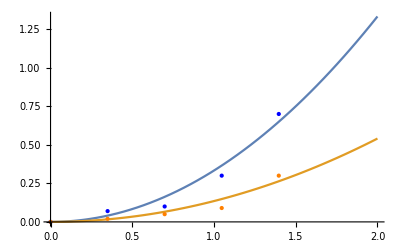

0.333149

0.135161

```mathematica
wristStiff={{0,0.34906585,0.698131701,1.047197551,1.396263402},{0,0.07,0.1,0.2,0.7},{0,0.02,0.05,0.09,0.3}};ext=Table[{wristStiff[[1,i]],wristStiff[[2,i]]},{i,1,5}];
flex=Table[{wristStiff[[1,i]],wristStiff[[3,i]]},{i,1,5}];
kEnM=Fit[ext,{x^2},x];
kFnM=Fit[flex,{x^2},x];
Plot[{kEnM,kFnM},{x,0,2},Epilog->{Blue,PointSize->Large,Point/@ext,Orange,Point/@flex}]
Ke=Coefficient[kEnM,x,2]
Kf=Coefficient[kFnM,x,2]
```

```mathematica
Wrist[ke_,kf_,be_,bf_,m_]:=DynamicModule[{},Refresh[{
dt=.1;
u={0,0};
v={0,0};
a={0,0};
f={0,0};
count=0;
timer={};
ph={0,0};
U={{0,u[[1]]}};
V={{0,v[[1]]}};
A={{0,a[[1]]}};
F={{0,f[[1]]}};
FF=F;
uF=F;
uE=F;
fesP={};
fesN={};
fsp={0,0};
fsn={0,0};
fsP={0,0};
fsN={0,0};

If[ϕ>Pi/2,ϕ=Pi/2];
If[ϕ<-Pi/2,ϕ=-Pi/2];

{Dynamic[Refresh[
count=count+dt;
timer=Append[timer,count];
If[u[[2]]<Pi/2-0.2&&u[[2]]>-Pi/2+0.2,k=0];
If[u[[2]]>Pi/2-0.2,k=ke;B=f[[1]]*be/1000];
If[u[[2]]<Pi/2+0.2,k=kf;B=f[[1]]*bf/1000];
a1=6*m/dt^2+3*B/dt;
a2=6*m/dt+2*B;
a3=2*m+dt*B/2;
ph[[2]]=f[[1]]+a1*u[[1]]+a2*v[[1]]+a3*a[[1]];
kh=k+a1;
u[[2]]=(ph[[2]]/kh+u[[1]])/2;
v[[2]]=(3/dt*(u[[2]]-u[[1]])-2*v[[1]]-dt*a[[1]]/2+v[[1]])/2;
a[[2]]=(6/dt^2*(u[[2]]-u[[1]])-6/dt*v[[1]]-2*a[[1]]+a[[2]])/2;
dist=ϕ-u[[2]];
dx=dist*frc;
f[[2]]=(2*m*(dx-v[[2]]*dt)/dt^2+f[[1]])/2;
If[u[[2]]>Pi/2,u[[2]]=Pi/2];
If[u[[2]]<-Pi/2,u[[2]]=-Pi/2];
If[u[[2]]==Pi/2||u[[2]]==-Pi/2,v[[2]]=0;a[[2]]=0];
θ=u[[2]]+Pi/2;
l=0.05;
ut={count,u[[2]]};
vt={count,v[[2]]};
at={count,a[[2]]};
ft={count,f[[2]]};
ff={count,f[[2]]/100};
ue={count,ff[[2]]/(1-c)};
uf={count,-c*ue[[2]]};
uE=Append[uE,ue];
uF=Append[uF,uf];
If[(Abs[f[[2]]-f[[1]]]>50&&f[[2]]>0),fsp={count,0,count,1,count,0};fesP=Append[fesP,fsp];
fsP=ArrayReshape[Flatten[fesP],{Length[fesP]*3,2}]];
If[(Abs[f[[2]]-f[[1]]]>50&&f[[2]]<0),fsn={count,0,count,-1,count,0};fesN=Append[fesN,fsn];fsN=ArrayReshape[Flatten[fesN],{Length[fesN]*3,2}]];
U=Append[U,ut];
V=Append[V,vt];
A=Append[A,at];
F=Append[F,ft];
FF=Append[FF,ff];
u[[1]]=u[[2]];v[[1]]=v[[2]];a[[1]]=a[[2]];f[[1]]=f[[2]];
Graphics3D[{Tube[{{0,0,0},{0,0,l}}],Tube[{{0,0,l},{.05*Cos[θ],0,l+Sin[θ]*.05}}],Tube[{{0,0,l},{.045*Cos[θ],0.02,l+Sin[θ]*.045}}],Tube[{{0,0,l},{.045*Cos[θ],-0.02,l+Sin[θ]*.045}}],Tube[{{0,0,l},{.035*Cos[θ],0.035,l+Sin[θ]*.035}}],Tube[{{0,0,l},{.035*Cos[θ],-0.035,l+Sin[θ]*.035}}]},PlotRange->{{-.05,.05},{-.05,.05},{0,l+.05}}, ImageSize->{scale}],
TrackedSymbols:>{},UpdateInterval->dt]]},
scale=125;
ϕ=0;
ToString[" Set Angle "]Dynamic[ϕ],
Slider[Dynamic[ϕ],{-Pi/2,Pi/2,.1}],
ToString["
Angle "]Dynamic[N[u[[1]],2]],
Dynamic[ListPlot[U,Joined-> True,PlotRange->{{count-5,count},{-Pi/2,Pi/2}},ImageSize->scale]],
ToString["Velocity "]Dynamic[Chop[N[v[[2]],2]]],
Dynamic[ListPlot[V,Joined-> True,PlotRange->{{count-5,count},{-10,10}},ImageSize->scale]],
ToString["Accel "]Dynamic[Chop[N[a[[2]],2]]],
Dynamic[ListPlot[A,Joined-> True,PlotRange->{{count-5,count},{-50,50}},ImageSize->scale]],
ToString["
Frc "]Dynamic[Chop[N[ff[[2]],2]]],
Dynamic[ListPlot[{FF,uE,uF},Joined-> True,PlotRange->{{count-5,count},{-30,30}},ImageSize->scale]],
ToString["FES "]Dynamic[fsp[[1]]],Dynamic[fsn[[1]]],
Dynamic[ListPlot[{fsP,fsN},Joined->True,PlotRange->{{count-3,count},{-1.1,1.1}}]],
ToString["
Force Multiplier
"]Dynamic[frc],
Slider[Dynamic[frc],{0,2,.1}],
ToString["
Flexor Extensor Ratio, (uF/uE)
"]Dynamic[c],
Slider[Dynamic[c],{0,.95,.05}],
ToString["
Timer "]Dynamic[count]

}]]
```

```mathematica
Wrist[.33,.15,3,3,5]
```